## RootFind Distilled

```mathematica
mSz=15;
nDim=3;
divNum=10;
divLst=ConstantArray[divNum,nDim];
title=MaTeX["M="<>ToString[mSz],Magnification->titleMag];
```

```mathematica
title
```

-Graphics-

```mathematica
fName="NLstRootfind_N_"<>ToString[mSz]<>"_res_"<>ToString[divNum]<>".jld2";
```

```mathematica
NmeanLst=readJuliaVar[fName,"NMeanLst"];
thresSz=readJuliaVar[fName,"thresSz"];
szRatLst=readJuliaVar[fName,"szRatLst"];
```

```mathematica
NmeanLst=NmeanLst//Flatten;
szLst=thresSz szRatLst//Flatten;
```

```mathematica
NmeanLst
```

{1719.06,1326.87,1248.09,1220.24,1207.54,1200.41,1196.6,1193.99,1192.08,1190.67,1189.69,1188.94,1188.22,1187.74,1187.26,1186.94,1186.64,1186.37,1186.28,1186.1,1185.96,1185.76,1185.65,1185.56,1185.52,1185.46,1185.42,1185.34,1185.25,1185.18,1185.14,1185.09,1185.01,1184.99,1184.92,1184.89,1184.86,1184.85,1184.82,1184.79,1184.79,1184.77,1184.77,1184.76,1184.76,1184.74,1184.73,1184.72,1184.71,1184.67}

```mathematica
szLst//Dimensions
```

{50}

```mathematica
nlm=NonlinearModelFit[{szRatLst//Flatten,NmeanLst}ᵀ,A Exp[-x/r]+A0,{A,r,A0},x];
```

```mathematica
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 1799. | 67.9003 | 26.4947 | 6.62894×10^-30
r | 8.16781 | 0.223009 | 36.6254 | 3.27946×10^-36
A0 | 1187.45 | 0.857455 | 1384.86 | 5.1476×10^-110

```mathematica
fName
```

NLstRootfind_N_10_res_15.jld2

```mathematica
NmeanLst//Dimensions
```

{1,50}

```mathematica
thresSz szRatLst⟦1⟧
```

{1.×10^-8}

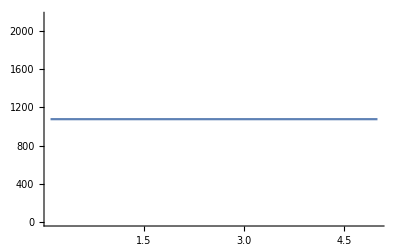

```mathematica
Plot[1077,{x,thresSz szRatLst⟦1,1⟧,thresSz szRatLst⟦-1,1⟧}]
```

```mathematica
xyLabs=MaTeX[#,Magnification->labMag]&/@{"d_{\\rm thres}","g_{\\rm deg}"};
```

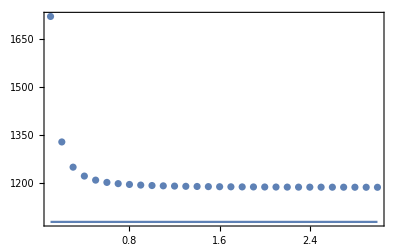

```mathematica
Show[{ListPlot[{(thresSz*szRatLst//Flatten)⟦1;;30⟧,(NmeanLst//Flatten)⟦1;;30⟧}ᵀ],Plot[1077,{x,thresSz szRatLst⟦1,1⟧,thresSz szRatLst⟦30,1⟧}]},PlotRange->All,Axes->False,Frame->True,BaseStyle->texStyle,FrameLabel->xyLabs,ImageSize->{Automatic,6cm},PlotLabel->title]
```

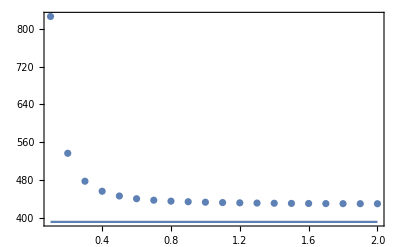

```mathematica
iEnd=20;
gWWE=391;
gWWEexp=436;
Show[{ListPlot[{(thresSz*szRatLst//Flatten)⟦1;;iEnd⟧,(NmeanLst//Flatten)⟦1;;iEnd⟧}ᵀ],Plot[gWWE,{x,thresSz szRatLst⟦1,1⟧,thresSz szRatLst⟦iEnd,1⟧}](*,Plot[gWWEexp,{x,thresSz szRatLst⟦1,1⟧,thresSz szRatLst⟦iEnd,1⟧}]*)},PlotRange->All,Axes->False,Frame->True,BaseStyle->texStyle,FrameLabel->xyLabs,ImageSize->{Automatic,6cm},PlotLabel->title]
```

```mathematica
szRatLst//Dimensions
```

{20,1}

```mathematica
thresSz
```

1.×10^-9

## Read in

```mathematica
fMain="deg_collisionPurified";
attrLst=attrLstBaseDim~Join~{"divColl"}~Join~{"bndThrRat"};
fMod="rootFind";
```

```mathematica
dim=3;
mSz=10;
divLst={10,10,10};
divColl=30;
bndThrRat=0.1;
itNum=100;
seed=1000;
valLst={dim,mSz,divLst,itNum,seed,divColl,bndThrRat};
```

```mathematica
fName=fNameFun[fMain,attrLst,valLst,fMod,jld2Type];
```

```mathematica
fName
```

deg_collisionPurified_dim_3_N_10_param_divide_[10, 10, 10]_instanceNum_100_seed_1000_divColl_30_bndThrRat_0.1_rootFind.jld2

```mathematica
fidlAllLstPol=readJuliaVar[fName,"fidlLstAllPol"];
```

```mathematica
fidlAllLstPol30=readJuliaVar[fName,"fidlLstAllPol"];
```

```mathematica
fidlAllLstPol//Dimensions
```

{2,1,9,1}

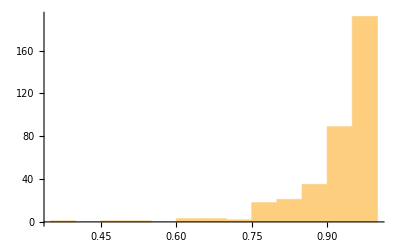

```mathematica
Histogram[fidlLstM2,Automatic]
```

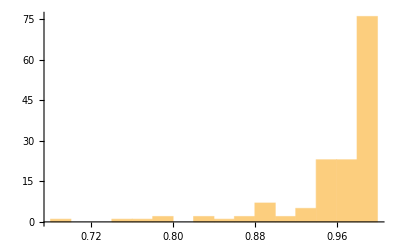

```mathematica
Histogram[fidlLstM1,Automatic]
```

```mathematica
fidlLstM2=fidlAllLstPol⟦1,1,2,1⟧//Flatten;
```

```mathematica
fidlLstM1=fidlAllLstPol⟦1,1,1,1⟧//Flatten;
```

```mathematica
attrLst
```

{dim,N,param_divide,instanceNum,seed,divColl,bndThrRat}

```mathematica
fidlLst30M1=fidlAllLstPol30⟦1,1,1,1⟧//Flatten;
```

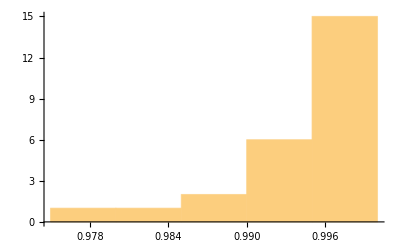

```mathematica
Histogram[fidlLst30M1,Automatic]
```